# Report Project Signal Processing

Course code: II1303
Date: 2021-11-29

Natasha Donner, ndonner@kth.se
Magnus Tomsic, mtomsic@kth.se
Mohamad Abou Helal, mohamaah@kth.se

Task 1:

## Summery

### Task

A mobile station is moving along a straight line, away from a base-station at position d = 0.  The base-station antenna is at 30 m above the ground and the mobile antenna is at 1,5 m high. As seen by the picture the mobile is receiving two signals one direct ray and one reflected. Assume that the reflection is perfect which means no power loss at the reflection, but a phase shift of π (reflection coefficient ρ = −1).
 
 a) Neglect the propagation loss due to the distance. The received signal in this case is written:
 
Received signal without propagation loss 
 r(t)=(t- τ_1)+p*s(t-τ_2) = s(t-τ_1)-s(t-τ_2)
 
Transmitted signal as it leaves base station
s(t) = cos(2 π f_c t) 

Carrier frequency 
f_c = 500 MHz

t is time in seconds

τ_1 = time delay of directed path 
τ_2  =  time delay of reflected path 

1. Write the received signal in the form A Cos[2 π f_c t+ϕ]
where A(d) and  ϕ (d). Where d is the distance between transmitter and receiver. 
2. Express the power of the received signal as a function of d. 
3. Plot the power of the received signal as a function of d when the mobile is moving from 0 - 2 km. Plot two 
different plots. First in linear scale Pr(d) in Watts and then in dBscale Pr(d) in dBW. 

P_r(d)=λ^2/(4π)^2 A^2(d)
P_r(d)|__dB=10log_10(Pr(d))dbW 

b) Repeat part a) taking into account this propagation loss.

P_r(d)=λ^2/((4π)^2 d^2)A^2(d)

### Result

#### Task 1

##### a)

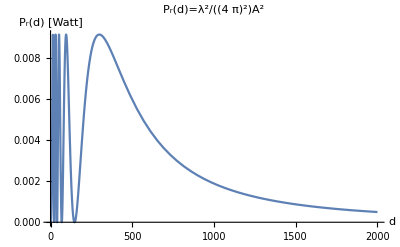
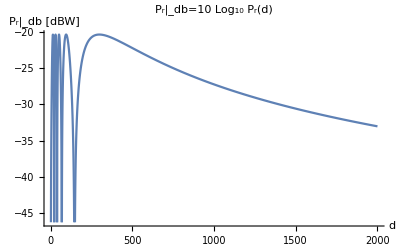
Time delay directed path
 τ_1 = (√((28,5)^2 + d^2))/c 
Time delay reflected path
 τ_2= (√((31,5)^2 + d^2))/c    
ω_0=2 π f_c
ϕ_1=τ_1(-ω_0)
ϕ_2=τ_2 (-ω_0)  

Distance to base station =  d  
Speed of light = c =  3x 10^8  

Received signal = r(t) = cos(2π(5 · 10^8)(t − τ_1))− cos(2π(5 · 10^8)(t− τ_2))
  
Amplitude depending on d = A(d) = √(√((Sin[ϕ_1]-Sin[ϕ_2])^2+(Cos[ϕ_1]-Cos[ϕ_2])^2)) 
Phase shift depending on d  = ϕ(d) = tan^-1[(Sin[ϕ_1]-Sin[ϕ_2])/(Cos[ϕ_1]-Cos[ϕ_2])]    
 r(t):=A Cos[2 π f_c t+ϕ]

λ=c/f_c    
P_r(d)=λ^2/(4 π)^2 A^2(d)

See section Code to follow all the steps that led to the plots. 

Fig1. 
-Graphics-

Fig2. 

-Graphics-

##### b

Fig 3

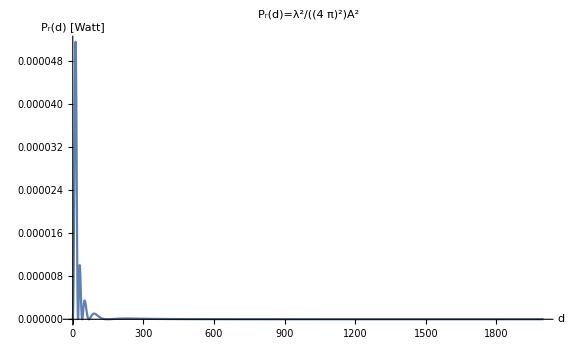

Fig 4

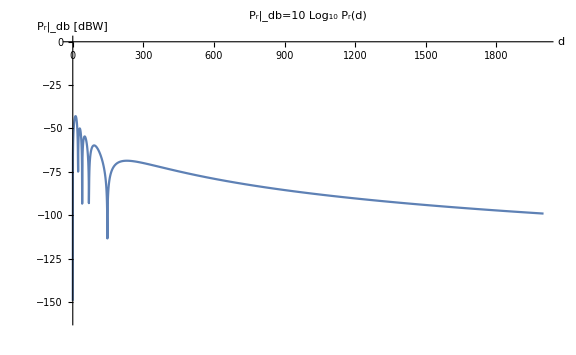

### Discussion

As a consequence of the height of the two antennas, the base station 30 m above ground and the mobile station at 1,5 m, we therefore know that the direct path has a length of 28,5 m and the reflected path has a length of 31,5 m at the start location d = 0. Pythagoras theorem is used to calculate this, and also to calculate the time delay τ_1 and 
τ_2. See code section. 

As seen in Fig 1, there is a significant drop in amplitude after 500m. It’s possible to both receive and send data from 0 - 2000 km.

## Code

```mathematica
ClearAll["Global`*"]
```

```mathematica
Subscript[y, t]=30;  (* hight of transmitter in m, base-station antenna *)
Subscript[y, m]=1.5; (* hight of receiver in m, mobile antenna *)
Subscript[d, 1]=√(d^2+(Subscript[y, t]-Subscript[y, m])^2);   (* direct distance *)
Subscript[d, 2]=√(d^2+(Subscript[y, m]+Subscript[y, t])^2);   (* Reflected distance *)
c=3 10^8;                           (* speed of light *)
Subscript[τ, 1]=Subscript[d, 1]/c;     (* time delay directed path *)
Subscript[τ, 2]=Subscript[d, 2]/c; (* time delay reflected path *)
Subscript[f, c]=5 10^8; (* 500 MHz  *)
Subscript[ω, 0]=2 π Subscript[f, c];    (*Different way to write omega *)
Subscript[ϕ, 1]=Subscript[τ, 1](-Subscript[ω, 0]);  (* Phi 1 *)
Subscript[ϕ, 2]=Subscript[τ, 2] (-Subscript[ω, 0]);  (* Phi 2 *)
λ=c/Subscript[f, c];   
A=√((Sin[Subscript[ϕ, 1]]-Sin[Subscript[ϕ, 2]])^2+(Cos[Subscript[ϕ, 1]]-Cos[Subscript[ϕ, 2]])^2);  (*Amplitude where A depends on d*)
ϕ=ArcTan[(Sin[Subscript[ϕ, 1]]-Sin[Subscript[ϕ, 2]])/(Cos[Subscript[ϕ, 1]]-Cos[Subscript[ϕ, 2]])];    (*to get angle phase *)
r[_t]:=A Cos[2 π Subscript[f, c] t+ϕ]; 
Subscript[P, r]=λ^2/(4 π)^2 A^2;
Plot[Subscript[P, r],{d,0,2000},AxesLabel->{"d","P_r(d) [Watt]"},PlotLabel->"P_r(d)=λ^2/(4  π)^2A^2"]
Plot[10Log10[Subscript[P, r]],{d,0,2000},AxesLabel->{"d","P_r|_db [dBW]"},PlotLabel->"P_r|_db=10 Log_10 P_r(d)"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
b)
```

```mathematica
Subscript[P, rb]=λ^2/((4 π)^2 d^2)A^2;
Plot[Subscript[P, rb],{d,0,2000},ImageSize->Large,PlotRange->Full,AxesLabel->{"d","P_r(d) [Watt]"},PlotLabel->"P_r(d)=λ^2/(4  π)^2A^2"]
Plot[10Log10[Subscript[P, rb]],{d,0,2000},ImageSize->Large,PlotRange->{-160,0.01},AxesLabel->{"d","P_r|_db [dBW]"},PlotLabel->"P_r|_db=10 Log_10 P_r(d)"]
```

-Graphics-

-Graphics-

Task 2:

## Summery

### Task

Examine the effect of sampling. Consider the signal

x(t)=|sin(2π f_0 t)|
f_0=220 Hz
T_0=(1/f_0)/2

a) Use the method "play" and explain the sound studying the complex Fourier series .

```mathematica
1/Subscript[T, 0]=∫_0^Subscript[T, 0] x(t)ⅇ^(-j(2π/Subscript[T, 0])k t)ⅆt
```

b) Play the sound using the sampling frequency 8000 Hz . What are the frequencies you will hear?

c) Play the sound using the sampling frequency 1000 Hz . What frequencies will you hear now?

d) Draw the correct spectrum in these two cases!

### Result

-Graphics-

-Graphics-

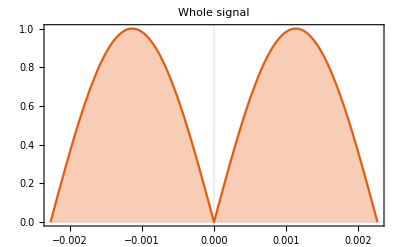

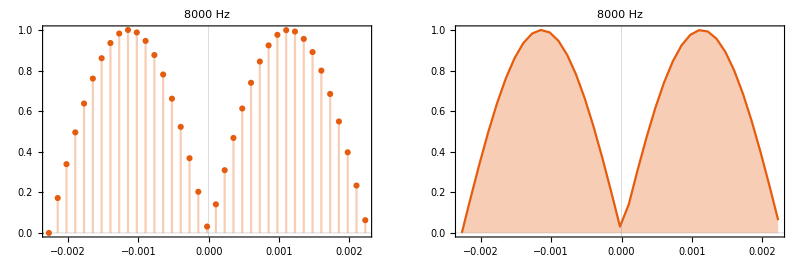

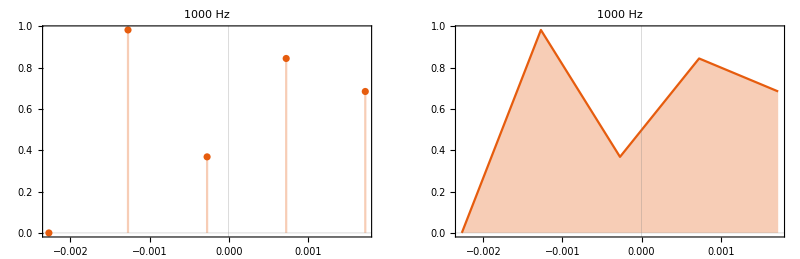

Animation of the signal when the sample rate increases from 220 Hz to 20 000 Hz

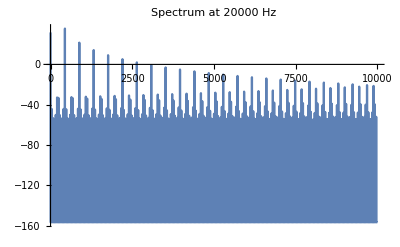

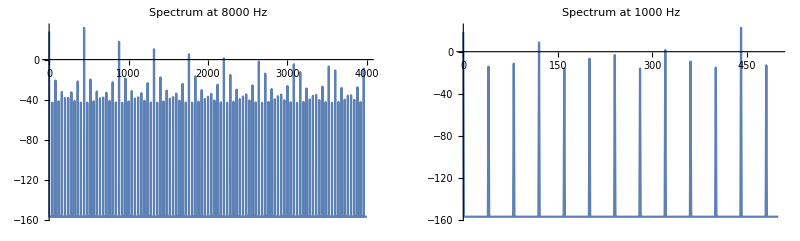

### Discussion

Since the play method use the same function, the original analog signal is the same. When we sample the sound with two different sample rates, the sound that will play will be different. We get a higher pitch when we sample with 8000Hz rather-than 1000Hz. 

With a sample rate of 8000 Hz we get a more precise sample because we will have more sample points. 

Nyquist theorem tells the frequency with which a wave motion must be measured using sampling in order to reproduce signals. The theorem is roughly that in order to avoid errors, one must sample with a frequency that is at least double the bandwidth signals, otherwise the results from the measurement will be lower than the actual frequency of the signal.
If we would have a regular Sin wave without the absolute value, it would  be possible to sample the sound at 2 x frequency, and still reproduce the right sound.

## Code

```mathematica
ClearAll["Global`*"]
```

```mathematica
f0=220;
```

```mathematica
T0=(1/f0)/2;
```

```mathematica
x[t_]:=Abs[Sin[2 π f0 t]]
```

```mathematica
ak=FullSimplify[1/T0∫_0^T0 x[t] ⅇ^(-ⅈ(2π/T0)k t)ⅆt]
```

(1+ⅇ^(-2 ⅈ k π))/(π-4 k^2 π)

```mathematica
Play[x[t],{t,0,1},SampleRate->8000]
Play[x[t],{t,0,1},SampleRate->1000]
```

-Graphics-

-Graphics-

```mathematica
pXt=Plot[x[t],{t,-(1/2)/f0,(1/2)/f0},PlotTheme->"Scientific", PlotLabel->"Whole signal",Filling->Axis]
dpXt8k=DiscretePlot[x[t],{t,-(1/2)/f0,(1/2)/f0,1/8000},PlotTheme->"Scientific",PlotLabel->"8000 Hz"];
dpXt8kj=DiscretePlot[x[t],{t,-(1/2)/f0,(1/2)/f0,1/8000},PlotTheme->"Scientific",PlotLabel->"8000 Hz",Joined->True];
dpXt1k=DiscretePlot[x[t],{t,-(1/2)/f0,(1/2)/f0,1/1000},PlotTheme->"Scientific", PlotLabel->"1000 Hz"];
dpXt1kj=DiscretePlot[x[t],{t,-(1/2)/f0,(1/2)/f0,1/1000},PlotTheme->"Scientific", PlotLabel->"1000 Hz",Joined->True];
GraphicsRow[{dpXt8k,dpXt8kj}]
GraphicsRow[{dpXt1k,dpXt1kj}]
Animate[DiscretePlot[x[t],{t,-(1/2)/f0,(1/2)/f0,1/s},PlotStyle->{ PointSize[0.01]},Joined->True],{s,10,20000},AnimationRunning->False,AnimationRate->300]
pdgXt20k=Periodogram[Play[x[t],{t,0,1},SampleRate->20000],PlotLabel->"Spectrum at 20000 Hz"]
pdgXt8k=Periodogram[Play[x[t],{t,0,1},SampleRate->8000],PlotLabel->"Spectrum at 8000 Hz"];
pdgXt1k=Periodogram[Play[x[t],{t,0,1},SampleRate->1000],PlotLabel->"Spectrum at 1000 Hz"];
GraphicsRow[{pdgXt8k,pdgXt1k}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

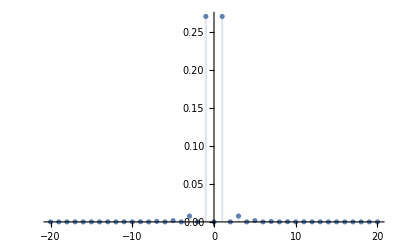

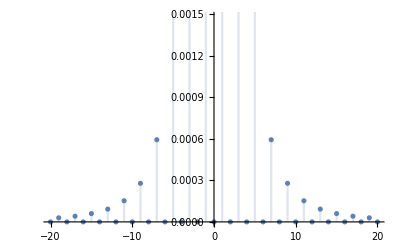

```mathematica
FSCa[k_]:=FourierSinCoefficient[ak,t,k]
DiscretePlot[Abs[FSCa[k]],{k,-20,20},PlotRange->All]
DiscretePlot[Abs[FSCa[k]],{k,-20,20},PlotRange->Automatic]
```